## Exponentials, why are they different

```mathematica
F[x_,"x"]=x;
F[x_,"x^2"]=x^2;
F[x_,"x^5"]=x^5;
F[x_,"e^x"]=Exp[x];
```

```mathematica
Col["x"]=Green;
Col["x^2"]=Pink;
Col["x^5"]=Red;
Col["e^x"]=Blue;
```

```mathematica
Manipulate[Plot[{F[x,"x"],F[x,"x^2"],F[x,"x^5"],F[x,"e^x"]},{x,0,a},PlotRange->All,PlotStyle->{Directive[Thick,Green],Directive[Thick,Pink],Directive[Thick,Red],Directive[Thick,Blue]}],{a,1,20}]
```

```mathematica
Manipulate[Plot[F[x,opt],{x,0,a},PlotRange->All,PlotStyle->{Col[opt],Thick}],{a,1,100},{opt,{"x","x^2","x^5","e^x"}},SaveDefinitions->True]
```

```mathematica
Export["manipulateExp.avi",m]
```

manipulateExp.avi

```mathematica
Log[10]/0.9
```

2.55843

## Phase space I vs S

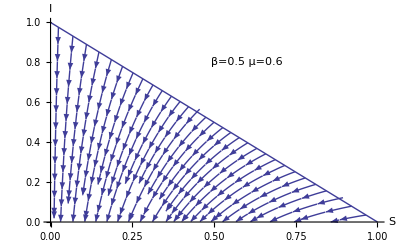

```mathematica
β = 0.5;
μ = 0.6;
Show[Plot[1-x,{x,0,1},AxesLabel->{"S","I"}],Graphics[Text[Style["β=0.5 μ=0.6",Large],{0.6,0.8}]],StreamPlot[{-β II S, (β II S - μ II)}, {S, 0, 1}, {II,0, 1}, AxesLabel -> {"S", "I"},RegionFunction->Function[{x,y},x+y≤1]]]
```

## Long time limit

```mathematica
S0 = 1 - 0.001;
Manipulate[
 Plot[{Log[S0/Sinf], r0*(1 - Sinf)}, {Sinf, 0, S0}, 
  PlotRange -> {0, 3.0}], {r0, 0.5, 2.5}]
```

Plot::plln: Limiting value S0 in {Sinf, 0, S0} is not a machine-sized real number.

```mathematica
β = 0.5;
μ = 0.2;
```

```mathematica
s=NDSolve[{S'[t]==-β II[t]S[t],II'[t]==β II[t]S[t]-μ II[t],S[0]==0.995,II[0]==0.005},{S,II},{t,0,150.0}]
```

{{S→InterpolatingFunction[{{0.,150.}},<>],II→InterpolatingFunction[{{0.,150.}},<>]}}

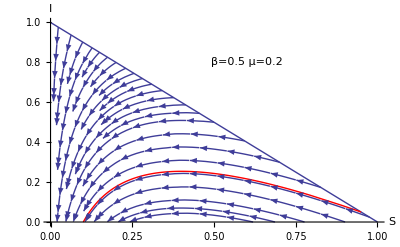

```mathematica
Show[Plot[1-x,{x,0,1},AxesLabel->{"S","I"}],Graphics[Text[Style["β=0.5 μ=0.2",Large],{0.6,0.8}]],StreamPlot[{-β II S, (β II S - μ II)}, {S, 0, 1}, {II,0, 1}, AxesLabel -> {"S", "I"},RegionFunction->Function[{x,y},x+y≤1]],ParametricPlot[Evaluate[{S[t],II[t]}/.s],{t,0,100},PlotRange->All,PlotStyle->{Thick,Red}]]
```

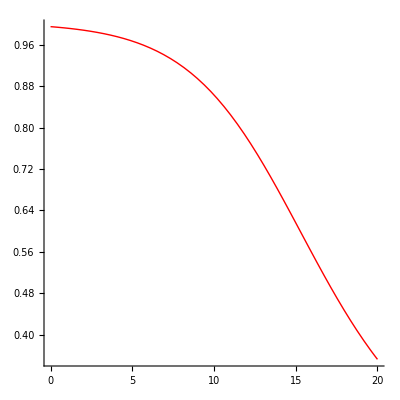

```mathematica
ParametricPlot[Evaluate[{t,S[t]}/.s],{t,0,20},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Thick,Red},AspectRatio->1]
```

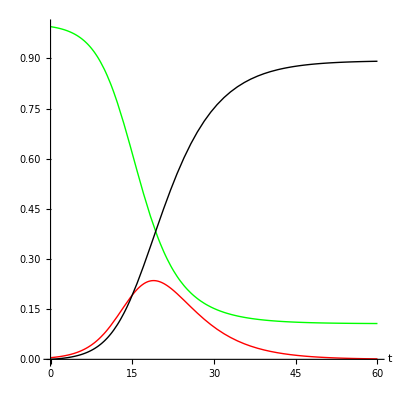

```mathematica
Show[ParametricPlot[Evaluate[{t,S[t]}/.s],{t,0,60},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Thick,Green},AspectRatio->1,AxesLabel->{"t",""}],ParametricPlot[Evaluate[{t,II[t]}/.s],{t,0,60},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Thick,Red},AspectRatio->1],ParametricPlot[Evaluate[{t,1-S[t]-II[t]}/.s],{t,0,60},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Thick,Black},AspectRatio->1]]
```